## converting the pdf to input.txt

```mathematica
file=First@FileNames["*.pdf",NotebookDirectory[]]
```

/Users/seantokunaga/Documents/Repositories/char-rnn/code civil early attempts/manual cleaned/LEGITEXT000006070721.pdf

```mathematica
text=Import[file, "Plaintext" ]
```

1281436
 |  |  |  |

```mathematica
text1prime=StringDrop[text, {1,104}];
```

```mathematica
(*Sort[StringPosition[text, "\nArticle "~~x_], #1⟦1⟧>#2⟦1⟧&]/.{x_, y_}-> {x-2,y+2}*)
```

```mathematica
(*text1=Fold[StringDrop[#1, #2]&, text,Sort[StringPosition[text, "Article "~~x_]/.{x_, y_}-> {x-2,y+2}, #1⟦1⟧>#2⟦1⟧&]];*)
```

```mathematica
text1= StringDelete[text1prime, "Dernière modification du texte le 01 janvier 2016 - Document généré le 06 janvier 2016 - Copyright (C) 2007-2016 Legifrance"]
```

1197810
 |  |  |  |

deleted all title and foot notes of the pdf. Now we can start working.

```mathematica
text2=StringSplit[text1, "\n"|" "]
```

{Article,1,,,,,Les,lois,et,,lorsqu'ils,sont,publiés,au,Journal,officiel,de,la,République,française,,les,actes,administratifs,entrent,en,vigueur,à,la,date,qu'ils,fixent,ou,,à,défaut,,222924,lots.,,,,,,Néanmoins,,les,créanciers,saisissants,exercent,leur,droit,sur,ladite,quote-part,,prise,dans,sa,consistance,au,moment,de,la,mutation,dont,le,prix,forme,l'objet,de,la,distribution.}
 |  |  |  |

```mathematica
StringLength@#&/@text2
```

{7,1,0,0,0,0,3,4,3,10,4,7,2,7,8,2,2,10,10,3,5,14,7,2,7,1,2,4,6,6,3,1,7,2,9,2,4,12,10,8,2,7,2,6,2,5,12,4,11,9,3,7,13,3,8,1,2,4,8,2,7,2,3,8,0,0,0,0,0,0,2,3,10,7,2,7,3,4,11,3,4,4,2,6,2,12,2,8,2,3,5,14,4,8,2,12,9,3,3,11,9,0,0,0,0,0,3,12,2,7,7,2,4,3,11,3,5,222756,2,7,2,7,11,5,4,5,2,10,3,10,3,3,9,6,1,7,4,2,9,6,9,3,12,2,7,6,0,0,0,0,0,0,0,7,1,1,13,6,0,7,4,0,0,0,0,4,3,7,2,4,12,3,11,11,6,7,3,3,4,9,4,8,6,2,6,2,2,11,4,8,2,3,6,3,2,10,3,7,8,9,4,3,5,0,0,0,0,0,10,3,10,11,8,4,5,3,6,11,5,4,2,11,2,6,2,2,8,4,2,4,5,7,2,2,13}
 |  |  |  |

```mathematica
text3 = Cases[text2, x_/;StringLength@x>0]
```

{Article,1,Les,lois,et,,lorsqu'ils,sont,publiés,au,Journal,officiel,de,la,République,française,,les,actes,administratifs,entrent,en,vigueur,à,la,date,qu'ils,fixent,ou,,à,défaut,,le,181436,dans,ces,lots.,Néanmoins,,les,créanciers,saisissants,exercent,leur,droit,sur,ladite,quote-part,,prise,dans,sa,consistance,au,moment,de,la,mutation,dont,le,prix,forme,l'objet,de,la,distribution.}
 |  |  |  |

```mathematica
text4=Fold[#1<>" "<>#2&, First@text3, Drop[text3, 1]];
```

```mathematica
StringTake[text4, 100]
```

Article 1 Les lois et, lorsqu'ils sont publiés au Journal officiel de la République française, les a

Here’s a way to get all the chapter titles. Use this sort of code to delete these cases.

```mathematica
text5=ReleaseHold@StringReplace[text4, Shortest["Chapitre"~~x__~~"Article"]->"Article"];
StringTake[text5, 1000]
```

Article 1 Les lois et, lorsqu'ils sont publiés au Journal officiel de la République française, les actes administratifs entrent en vigueur à la date qu'ils fixent ou, à défaut, le lendemain de leur publication. Toutefois, l'entrée en vigueur de celles de leurs dispositions dont l'exécution nécessite des mesures d'application est reportée à la date d'entrée en vigueur de ces mesures. En cas d'urgence, entrent en vigueur dès leur publication les lois dont le décret de promulgation le prescrit et les actes administratifs pour lesquels le Gouvernement l'ordonne par une disposition spéciale. Les dispositions du présent article ne sont pas applicables aux actes individuels. Article 2 La loi ne dispose que pour l'avenir ; elle n'a point d'effet rétroactif. Article 3 Les lois de police et de sûreté obligent tous ceux qui habitent le territoire. Les immeubles, même ceux possédés par des étrangers, sont régis par la loi française. Les lois concernant l'état et la capacité des personnes régissent

Now try to get rid of sections

```mathematica
text6=ReleaseHold@StringReplace[text5, Shortest["Section"~~x__~~"Article"]->"Article"];
StringTake[text6, 1000]
```

Article 1 Les lois et, lorsqu'ils sont publiés au Journal officiel de la République française, les actes administratifs entrent en vigueur à la date qu'ils fixent ou, à défaut, le lendemain de leur publication. Toutefois, l'entrée en vigueur de celles de leurs dispositions dont l'exécution nécessite des mesures d'application est reportée à la date d'entrée en vigueur de ces mesures. En cas d'urgence, entrent en vigueur dès leur publication les lois dont le décret de promulgation le prescrit et les actes administratifs pour lesquels le Gouvernement l'ordonne par une disposition spéciale. Les dispositions du présent article ne sont pas applicables aux actes individuels. Article 2 La loi ne dispose que pour l'avenir ; elle n'a point d'effet rétroactif. Article 3 Les lois de police et de sûreté obligent tous ceux qui habitent le territoire. Les immeubles, même ceux possédés par des étrangers, sont régis par la loi française. Les lois concernant l'état et la capacité des personnes régissent

```mathematica
text7=ReleaseHold@StringReplace[text6, Shortest["Livre"~~x__~~"Article"]->"Article"];
StringTake[text7, 1000]
```

Article 1 Les lois et, lorsqu'ils sont publiés au Journal officiel de la République française, les actes administratifs entrent en vigueur à la date qu'ils fixent ou, à défaut, le lendemain de leur publication. Toutefois, l'entrée en vigueur de celles de leurs dispositions dont l'exécution nécessite des mesures d'application est reportée à la date d'entrée en vigueur de ces mesures. En cas d'urgence, entrent en vigueur dès leur publication les lois dont le décret de promulgation le prescrit et les actes administratifs pour lesquels le Gouvernement l'ordonne par une disposition spéciale. Les dispositions du présent article ne sont pas applicables aux actes individuels. Article 2 La loi ne dispose que pour l'avenir ; elle n'a point d'effet rétroactif. Article 3 Les lois de police et de sûreté obligent tous ceux qui habitent le territoire. Les immeubles, même ceux possédés par des étrangers, sont régis par la loi française. Les lois concernant l'état et la capacité des personnes régissent

```mathematica
text8=ReleaseHold@StringReplace[text7, Shortest["Paragraphe"~~x__~~"Article"]->"Article"];
StringTake[text8, 1000]
```

Article 1 Les lois et, lorsqu'ils sont publiés au Journal officiel de la République française, les actes administratifs entrent en vigueur à la date qu'ils fixent ou, à défaut, le lendemain de leur publication. Toutefois, l'entrée en vigueur de celles de leurs dispositions dont l'exécution nécessite des mesures d'application est reportée à la date d'entrée en vigueur de ces mesures. En cas d'urgence, entrent en vigueur dès leur publication les lois dont le décret de promulgation le prescrit et les actes administratifs pour lesquels le Gouvernement l'ordonne par une disposition spéciale. Les dispositions du présent article ne sont pas applicables aux actes individuels. Article 2 La loi ne dispose que pour l'avenir ; elle n'a point d'effet rétroactif. Article 3 Les lois de police et de sûreté obligent tous ceux qui habitent le territoire. Les immeubles, même ceux possédés par des étrangers, sont régis par la loi française. Les lois concernant l'état et la capacité des personnes régissent

```mathematica
text9=ReleaseHold@StringReplace[text8, Shortest["Sous-section"~~x__~~"Article"]->"Article"];
StringTake[text9, 1000]
```

Article 1 Les lois et, lorsqu'ils sont publiés au Journal officiel de la République française, les actes administratifs entrent en vigueur à la date qu'ils fixent ou, à défaut, le lendemain de leur publication. Toutefois, l'entrée en vigueur de celles de leurs dispositions dont l'exécution nécessite des mesures d'application est reportée à la date d'entrée en vigueur de ces mesures. En cas d'urgence, entrent en vigueur dès leur publication les lois dont le décret de promulgation le prescrit et les actes administratifs pour lesquels le Gouvernement l'ordonne par une disposition spéciale. Les dispositions du présent article ne sont pas applicables aux actes individuels. Article 2 La loi ne dispose que pour l'avenir ; elle n'a point d'effet rétroactif. Article 3 Les lois de police et de sûreté obligent tous ceux qui habitent le territoire. Les immeubles, même ceux possédés par des étrangers, sont régis par la loi française. Les lois concernant l'état et la capacité des personnes régissent

```mathematica
text10=StringDrop[ReleaseHold@StringReplace[text9, Shortest["Article"~~x__~~" "]->Hold@("\nArticle"<>x<>" : ")], 1];
StringTake[text10, 1000]
```

Article 1 : Les lois et, lorsqu'ils sont publiés au Journal officiel de la République française, les actes administratifs entrent en vigueur à la date qu'ils fixent ou, à défaut, le lendemain de leur publication. Toutefois, l'entrée en vigueur de celles de leurs dispositions dont l'exécution nécessite des mesures d'application est reportée à la date d'entrée en vigueur de ces mesures. En cas d'urgence, entrent en vigueur dès leur publication les lois dont le décret de promulgation le prescrit et les actes administratifs pour lesquels le Gouvernement l'ordonne par une disposition spéciale. Les dispositions du présent article ne sont pas applicables aux actes individuels. 
Article 2 : La loi ne dispose que pour l'avenir ; elle n'a point d'effet rétroactif. 
Article 3 : Les lois de police et de sûreté obligent tous ceux qui habitent le territoire. Les immeubles, même ceux possédés par des étrangers, sont régis par la loi française. Les lois concernant l'état et la capacité des personnes r

to get a bit of information out about the articles:

```mathematica
individualArticles=StringSplit[text10, "\n"];
First@individualArticles
individualArticles⟦2⟧
individualArticles⟦3⟧
```

Article 1 : Les lois et, lorsqu'ils sont publiés au Journal officiel de la République française, les actes administratifs entrent en vigueur à la date qu'ils fixent ou, à défaut, le lendemain de leur publication. Toutefois, l'entrée en vigueur de celles de leurs dispositions dont l'exécution nécessite des mesures d'application est reportée à la date d'entrée en vigueur de ces mesures. En cas d'urgence, entrent en vigueur dès leur publication les lois dont le décret de promulgation le prescrit et les actes administratifs pour lesquels le Gouvernement l'ordonne par une disposition spéciale. Les dispositions du présent article ne sont pas applicables aux actes individuels.

Article 2 : La loi ne dispose que pour l'avenir ; elle n'a point d'effet rétroactif.

Article 3 : Les lois de police et de sûreté obligent tous ceux qui habitent le territoire. Les immeubles, même ceux possédés par des étrangers, sont régis par la loi française. Les lois concernant l'état et la capacité des personnes régissent les Français, même résidant en pays étranger.

```mathematica
Length@individualArticles
```

2820

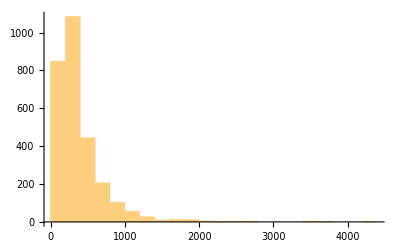

```mathematica
Histogram@(StringLength@#&/@individualArticles)
```

ideally I would want an rnn with a sequence length of about 400...

```mathematica
Export[ToFileName[{NotebookDirectory[]},"input.txt"],text10]
```

/Users/seantokunaga/Documents/Repositories/char-rnn/code civil early attempts/recleaned/input.txt